```mathematica
(*Chua circuit with a simple limiter where the x dimension limits itself*)
```

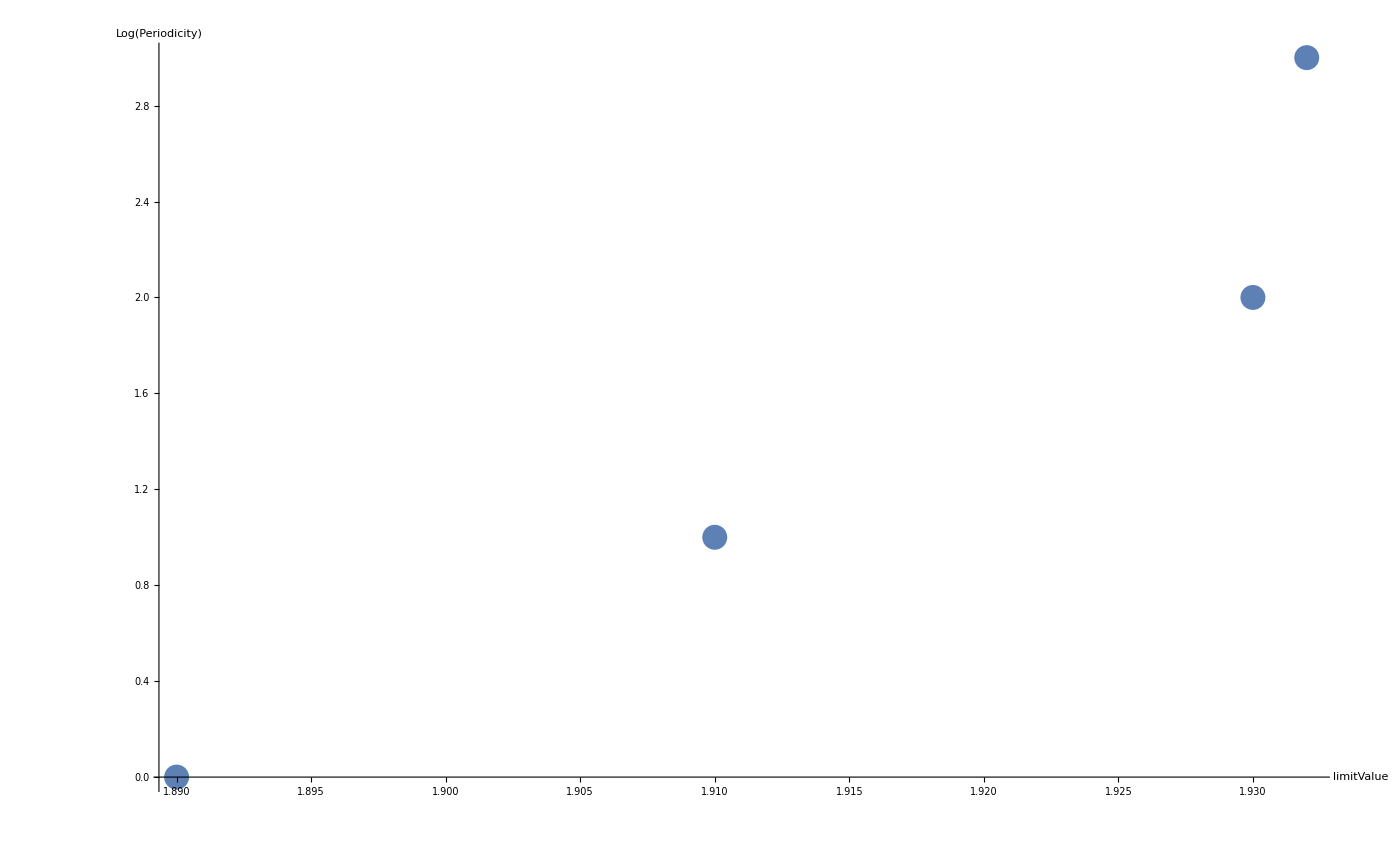

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/x-limits-x-periodicityParameters013below.png

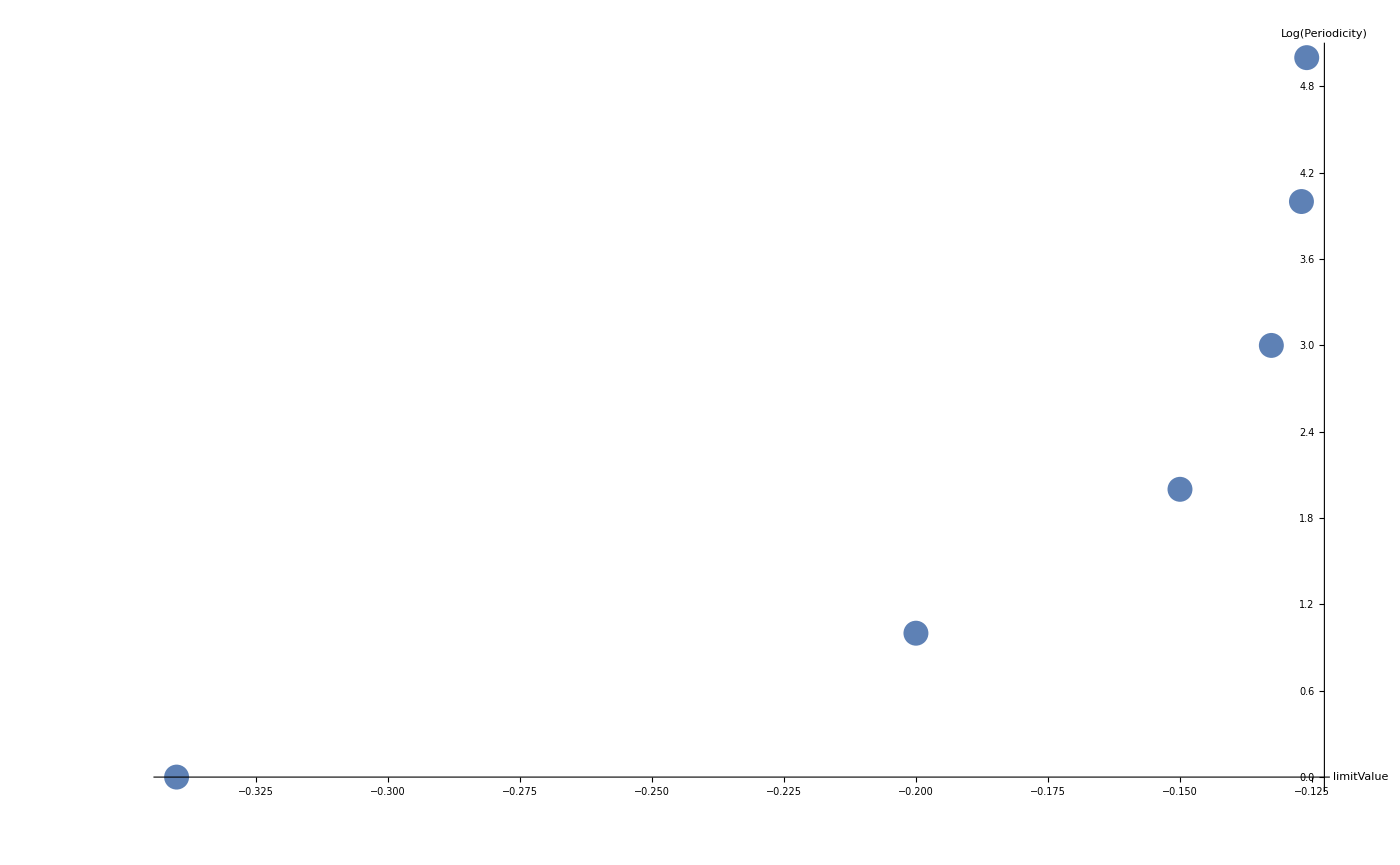

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/x-limits-x-periodicityParameters013above.png

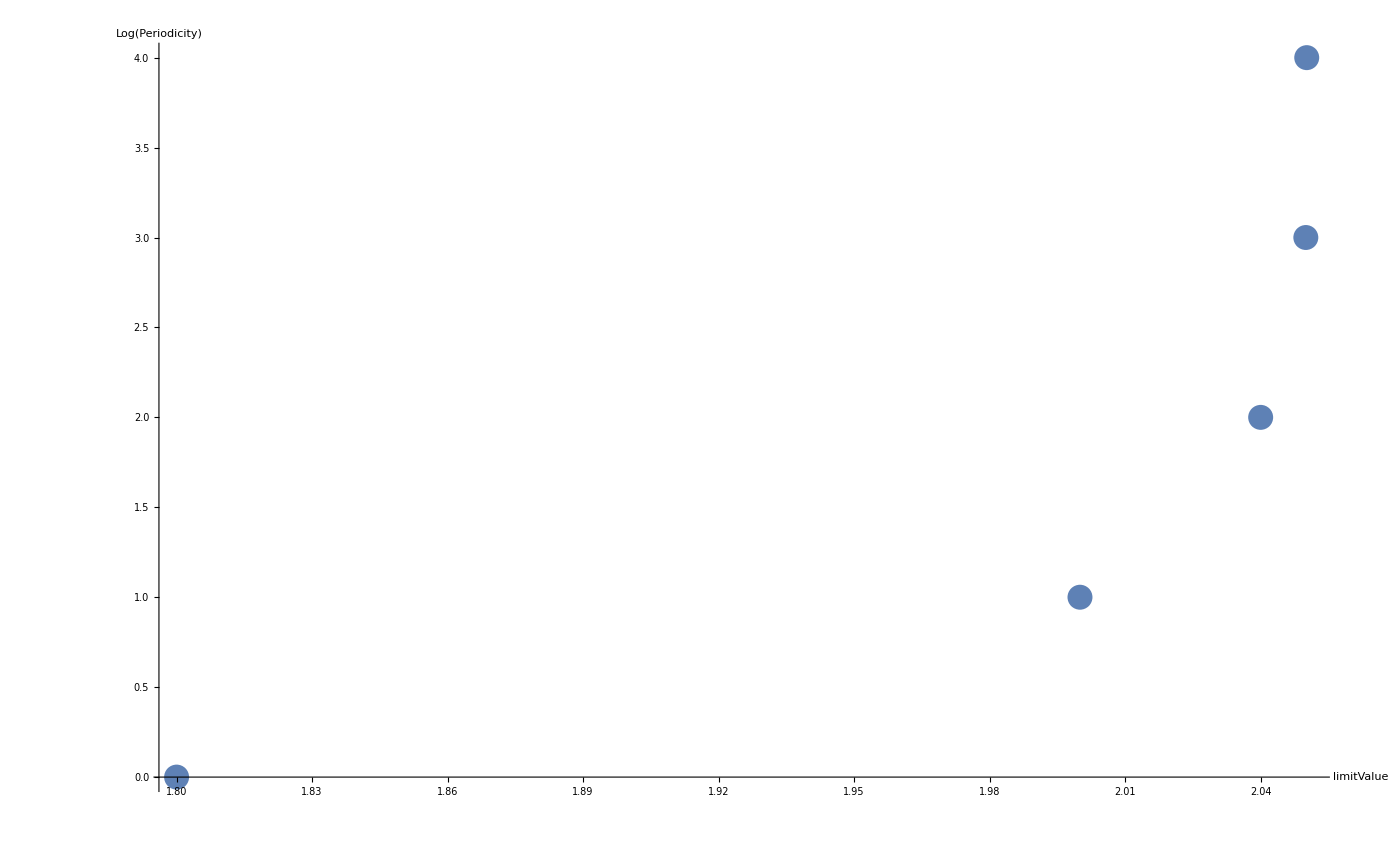

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/x-limits-x-periodicityParameters05below.png

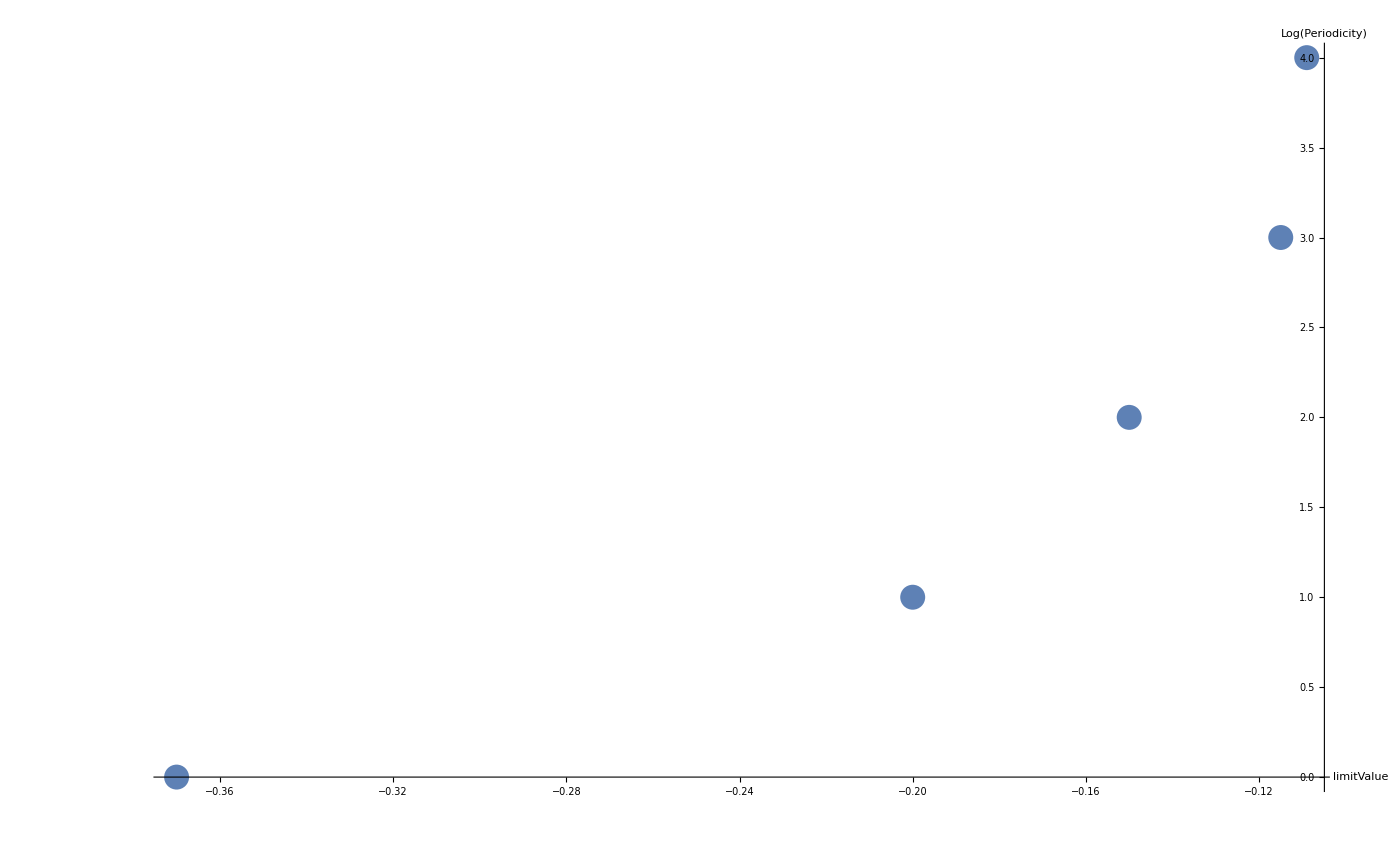

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/x-limits-x-periodicityParameters05above.png

```mathematica
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
f[{x_,y_,z_}]:={c1 * (y-x-g[x])limiter[x],c2*(x-y+z),-c3*y };

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/2];
k3=h*f[x+k2/2];
k4=h*f[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

RK6 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/4];
k3=h*f[x+(3.0/32.0)*k1+(9.0/32.0)*k2];
k4=h*f[x+(1932.0/2197.0)*k1-(7200.0/2197.0)*k2
+(7296.0/2197.0)*k3];
k5 = h *f[x+(439.0/216.0)*k1-8.0*k2+(3680.0/513.0)*k3
-(845.0/4104.0)*k4];
k6 = h * f[x-(8.0/27.0)*k1+2.0*k2-(3544.0/2565.0)*k3
+(1859.0/4104.0)*k4-(11.0/40.0)*k5];
y=x+(16.0/135.0)*k1+(6656.0/12825.0)*k3
+(28561.0/56430.0)*k4-(9.0/50.0)*k5+(2.0/55.0)*k6;
x = y;
Return[x]];

x ={-1.5,0,0};
c1=15.6;
c2 =1;
c3 = 28;
m0=-0.714; (*slope in outer region default:-0.714 *)
m1 = -1.143; (*slope in inner region /default: -1.143 *)
b =1; (*Breakpoints *)

limiter = softLim; (* Choose the softlimiter *)
limitValue =2;
	(* 
	For softness 0.5:
	1.8 / Period 1 limit cycle /
2 / Period 2 limit cycle /
 2.04 Period 4 limite cycle /
 2.05 Period 8 limit cycle /
 2.0502 Period 16 limit cycle /
2.06 /Very high period limit cycle/
  >2.18 / Double scroll chaos /
 High period limit cycle/ Chaos /
/Chaos /
 not limited /
*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

n =40000;

baseImagePath = NotebookDirectory[] <> "build/";

imageSize = 1400; (*Output image width*)
(*0.13*)
periodicityParameters013below = {{1.932,8},{1.93,4},{1.91,2},{1.89,1}};
periodicityParameters013below[[All,2]] =Log2[periodicityParameters013below[[All,2]]];
periodicityParameters013above ={{-0.126,32},{-0.127,16},{-0.1327,8},{-0.15,4},{-0.2,2},{-0.34,1}};
periodicityParameters013above[[All,2]] =Log2[periodicityParameters013above[[All,2]]];

(*0.5*)
periodicityParameters05below = {{2.0502,16},{2.05,8},{2.04,4},{2,2},{1.8,1}};
periodicityParameters05below[[All,2]] =Log2[periodicityParameters05below[[All,2]]];
periodicityParameters05above = {{-0.109,16},{-0.115,8},{-0.15,4},{-0.2,2},{-0.37,1}};
periodicityParameters05above[[All,2]] =Log2[periodicityParameters05above[[All,2]]];


 periodicity013belowPlot = ListPlot[periodicityParameters013below,ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"limitValue","Log(Periodicity)"}]
Export[baseImagePath<>"x-limits-x-periodicityParameters013below.png",periodicity013belowPlot,Background->None]
 periodicity013abovePlot = ListPlot[periodicityParameters013above,ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"limitValue","Log(Periodicity)"}]
Export[baseImagePath<>"x-limits-x-periodicityParameters013above.png",periodicity013abovePlot,Background->None]

 periodicity05belowPlot = ListPlot[periodicityParameters05below,ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"limitValue","Log(Periodicity)"}]
Export[baseImagePath<>"x-limits-x-periodicityParameters05below.png",periodicity05belowPlot,Background->None]
 perodicity05abovePlot = ListPlot[periodicityParameters05above,ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"limitValue","Log(Periodicity)"}]
Export[baseImagePath<>"x-limits-x-periodicityParameters05above.png",perodicity05abovePlot,Background->None]
```

```mathematica
BarLegend[{"TemperatureMap",{0,1}},LabelStyle->{FontSize->20}]
```

```mathematica
(*Unlimited-chua-circuit*)
imageName = "Unlimited-chua-circuit";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =50; (*Limit of the limiting dimension*)
limitCycleStable = 199000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.1; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-932";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.932; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-93";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.93; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-91";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.91; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-89";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.89; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-61";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.61; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-57";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.57; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-5";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.5; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-4";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.4; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-1-3";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.3; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-0-5";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =0.5; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13-0-26991";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =0.26991; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)+
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13--0-126";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.126; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13--0-127";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.127; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13--0-1327";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.1327; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13--0-15";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.15; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13--0-2";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.2; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-13--0-34";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.34; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5-2-0502";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.0502; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5-2-05";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.05; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5-2-04";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.04; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5-2";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5-1-8";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.8; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5--0-109";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.109; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5--0-115";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.115; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5--0-15";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.15; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5--0-2";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.2; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5--0-37";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.37; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-x-softness*)
imageName = "Limited-chua-circuit-x-softness-0-5--4";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =-4; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Bifurcation-plot-x-softness*)
imageName = "Bifurcation-plot-x-softness";

hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

c1=15.6;
c2 =1;
c3 = 28;
m0=-0.714; (*slope in outer region default:-0.714 *)
m1 = -1.143; (*slope in inner region /default: -1.143 *)
b =1; (*Breakpoints *)

n=200000;

limiter = softLim; (* Choose the softlimiter *)
limitValue =-0.126; (*Limit of the limiting dimension*)
limitCycleStable = 199000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50]

(*Define the chua circuit's differential equations *)
chua={
Derivative[1][x][t]==c1 * (y[t]-x[t]-g(m0 * x[t] + (m1-m0)/2 * (Abs[x[t]+b]-Abs[x[t]-b])))*limiter[x[t]],
Derivative[1][y][t]==c2*(x[t]-y[t]+z[t]),
Derivative[1][z][t]==-c3*y[t]};

poincaresection[{x0_,y0_,z0_}]:=Reap[NDSolve[{chua,x[0]==x0,y[0]==y0,z[0]==z0,WhenEvent[y[t]==0,Sow[{x[t],0}]]},{},{t,0,n},MaxSteps->∞]][[-1,1]]

sectdata=Map[poincaresection,{{-1.5,0,0}}];
ListPlot[sectdata,ImageSize->1400]
```

```mathematica
abc={Derivative[1][x][t]==3/4 Cos[y[t]]+Sin[z[t]],Derivative[1][y][t]==Cos[z[t]]+Sin[x[t]],Derivative[1][z][t]==Cos[x[t]]+3/4 Sin[y[t]]};

psect[{x0_,y0_,z0_}]:=Reap[NDSolve[{abc,x[0]==x0,y[0]==y0,z[0]==z0,WhenEvent[y[t]==0,Sow[{x[t],z[t]}]]},{},{t,0,1000},MaxSteps->∞]][[-1,1]]

abcdata=Mod[Map[psect,{{4.267682454609692,0,0.9952906114885919},{1.6790790859443243,0,2.1257099470901704},{2.9189523719753327,0,4.939152797323216},{3.1528896559036776,0,4.926744120488727},{0.9829282640373566,0,1.7074633238173198},{ymax090394012299985,0,4.170087631574883},{6.090600411133905,0,2.3736566160602277},{6.261716134007686,0,1.4987884558838156},{1.005126683795467,0,1.3745418575363608},{1.5880780704325377,0,1.3039536044289253},{3.622408133554125,0,2.289597511313432},{0.030948690635763183,0,4.306922133429981},{5.906038850342371,0,5.000045498132029}}],2 π];
ListPlot[abcdata,ImageSize->Medium]
```